```mathematica
Simplify [D[a*b*(x-1)f[x,t],{x,n}]]
```

a b Binomial[n,K[1]] ∂_{x,n-K[1]} f[x,t] (Piecewise[{{1, K[1]==1}, {0, True}}])K[1]0n

```mathematica
FullSimplify [D[a*b(s-1)G[s,t]+c(s-1)D[G[s,t],s],s]]
```

a b G[s,t]+(c+a b (-1+s)) G^(1,0)[s,t]+c (-1+s) G^(2,0)[s,t]

```mathematica
FullSimplify [D[a*b(s-1)G[s,t]+c(s-1)D[G[s,t],s],{s,2}]]
```

2 a b G^(1,0)[s,t]+(2 c+a b (-1+s)) G^(2,0)[s,t]+c (-1+s) G^(3,0)[s,t]

```mathematica
ExpandAll[D[a*b(s-1)G[s,t]+c(s-1)D[G[s,t],s],{s,n}]]
```

a b Binomial[n,K[1]] ∂_{s,n-K[1]} G[s,t] (Piecewise[{{1, K[1]==1}, {0, True}}])K[1]0n+c Binomial[n,K[1]] ∂_{s,n-K[1]} G^(1,0)[s,t] (Piecewise[{{1, K[1]==1}, {0, True}}])K[1]0n

```mathematica
(1-2z^2+z^4)D[G[z,t],{z,2}]+(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] + (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t])
```

(-1+L) L (-1+z^2)+d^2 (1-1/z^2) G[z,t]+(-1/z+(-3+2 L) z+(2-2 L) z^3) G^(1,0)[z,t]+(1-2 z^2+z^4) G^(2,0)[z,t]

```mathematica
Expand[D[(1-2z^2+z^4)D[G[z,t],{z,2}]+(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] + (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t]),{z,1}]]
```

-2 L z+2 L^2 z+(2 d^2 G[z,t])/z^3-3 G^(1,0)[z,t]+d^2 G^(1,0)[z,t]+2 L G^(1,0)[z,t]+(G^(1,0)[z,t])/z^2-(d^2 G^(1,0)[z,t])/z^2+6 z^2 G^(1,0)[z,t]-6 L z^2 G^(1,0)[z,t]-(G^(2,0)[z,t])/z-7 z G^(2,0)[z,t]+2 L z G^(2,0)[z,t]+6 z^3 G^(2,0)[z,t]-2 L z^3 G^(2,0)[z,t]+G^(3,0)[z,t]-2 z^2 G^(3,0)[z,t]+z^4 G^(3,0)[z,t]

```mathematica
Expand[D[(1-2z^2+z^4)D[G[z,t],{z,2}]+(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] + (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t]),{z,2}]]
```

-2 L+2 L^2-(6 d^2 G[z,t])/z^4-(2 G^(1,0)[z,t])/z^3+(4 d^2 G^(1,0)[z,t])/z^3+12 z G^(1,0)[z,t]-12 L z G^(1,0)[z,t]-10 G^(2,0)[z,t]+d^2 G^(2,0)[z,t]+4 L G^(2,0)[z,t]+(2 G^(2,0)[z,t])/z^2-(d^2 G^(2,0)[z,t])/z^2+24 z^2 G^(2,0)[z,t]-12 L z^2 G^(2,0)[z,t]-(G^(3,0)[z,t])/z-11 z G^(3,0)[z,t]+2 L z G^(3,0)[z,t]+10 z^3 G^(3,0)[z,t]-2 L z^3 G^(3,0)[z,t]+G^(4,0)[z,t]-2 z^2 G^(4,0)[z,t]+z^4 G^(4,0)[z,t]

```mathematica
FullSimplify[-2/z^3+(4 d^2)/z^3+12 z -12 L z  ]
```

(-2+4 d^2-12 (-1+L) z^4)/z^3

```mathematica
FullSimplify[-10 +d^2 +4 L +2/z^2-d^2/z^2+24 z^2 -12 L z^2  ]
```

-10+d^2+4 L+(2-d^2)/z^2-12 (-2+L) z^2

```mathematica
FullSimplify[-1/z-11 z +2 L z +10 z^3 -2 L z^3 ]
```

-1/z+(-11+2 L) z-2 (-5+L) z^3

```mathematica
Simplify[1-2 z^2 +z^4 ]
```

(-1+z^2)^2

```mathematica
FullSimplify[D[(1-2z^2+z^4)D[G[z,t],{z,2}]+(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] + (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t]),{z,2}]]
```

1/z^4(-6 d^2 G[z,t]+z (2 (-1+2 d^2-6 (-1+L) z^4) G^(1,0)[z,t]+z ((2-d^2+(-10+d^2+4 L) z^2-12 (-2+L) z^4) G^(2,0)[z,t]+z (2 (-1+L) L z+(-1+(-11+2 L) z^2-2 (-5+L) z^4) G^(3,0)[z,t]+z (-1+z^2)^2 G^(4,0)[z,t]))))

```mathematica
FullSimplify[D[(1-2z^2+z^4)D[G[z,t],{z,2}]+(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] + (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t]),{z,3}]]
```

1/z^5(24 d^2 G[z,t]+z (6 (1-3 d^2-2 (-1+L) z^4) G^(1,0)[z,t]+z (6 (-1+d^2+2 (5-3 L) z^4) G^(2,0)[z,t]+z ((3-d^2+(-21+d^2+6 L) z^2-18 (-3+L) z^4) G^(3,0)[z,t]+z ((-1+(-15+2 L) z^2-2 (-7+L) z^4) G^(4,0)[z,t]+z (-1+z^2)^2 G^(5,0)[z,t])))))

```mathematica
FullSimplify[D[(1-2z^2+z^4)D[G[z,t],{z,2}]+(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] + (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t]),{z,n}]]
```

(-1+L) (Piecewise[{{L z^(2-n) FactorialPower[2,n], n≥1}, {L (-1+z^2), True}}])+(1+d^2) ComplexInfinityK[1]0n+(z^(2-K[1]) ∂_{z,n-K[1]} G^(2,0)[z,t] Gamma[1+n] (-4+(24 z^2)/(12-7 K[1]+K[1]^2)))/(Gamma[3-K[1]] Gamma[1+n-K[1]] Gamma[1+K[1]])K[1]0n

```mathematica
FullSimplify[D[(1-2z^2+z^4)D[G[z,t],{z,2}],{z,1}]]
```

(-1+z^2) (4 z G^(2,0)[z,t]+(-1+z^2) G^(3,0)[z,t])

```mathematica
FullSimplify[D[(-1/z+(-3+2L)z+(2-2L)z^3)D[G[z,t],z] ,{z,1}]]
```

(-3+2 L+1/z^2-6 (-1+L) z^2) G^(1,0)[z,t]+(-1/z+(-3+2 L) z-2 (-1+L) z^3) G^(2,0)[z,t]

```mathematica
FullSimplify[D[ (L(L-1)(z^2-1)+d^2(1-1/z^2)G[z,t]),{z,1}]]
```

2 (-1+L) L z+(d^2 (2 G[z,t]+z (-1+z^2) G^(1,0)[z,t]))/z^3

```mathematica
(1+d^2) ComplexInfinityK[1]0n
```

(1+d^2) ComplexInfinityK[1]0n

### Solving simple mean equation

```mathematica
equation = x'[t]==((1-2L)x[t]+L(L-1)+d^2)/(L(L-1))
```

x'[t]==(d^2+(-1+L) L+(1-2 L) x[t])/((-1+L) L)

```mathematica
funkcija[t_]=FullSimplify[DSolveValue[equation,x,t][t]]/.{C[1]->1}
```

ⅇ^((t-2 L t)/((-1+L) L))+(d^2+(-1+L) L)/(-1+2 L)

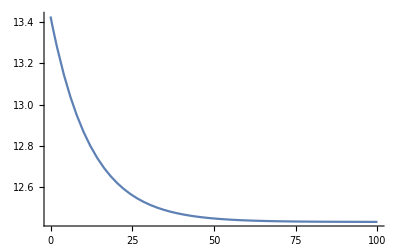

```mathematica
Plot[funkcija[t]/.{L->25,d->3},{t,0,100},PlotRange->All]
```

#### Fixing Initial Condition

```mathematica
funkcija2[t_]=FullSimplify[DSolveValue[{equation,x[0]==0},x,t][t]]
```

(ⅇ^(-(2 t)/(-1+L)) (ⅇ^((2 t)/(-1+L))-ⅇ^(t/((-1+L) L))) (d^2+(-1+L) L))/(-1+2 L)

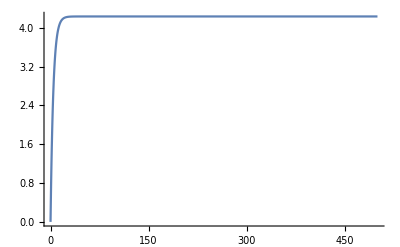

```mathematica
Plot[funkcija2[t]/.{L->9,d->0},{t,0,500},PlotRange->All]
```

```mathematica
funkcija2[t_]=FullSimplify[DSolveValue[{equation,x[0]==50},x,t][t]]
```

(d^2+(-1+L) L-ⅇ^((t-2 L t)/((-1+L) L)) (50+d^2+(-101+L) L))/(-1+2 L)

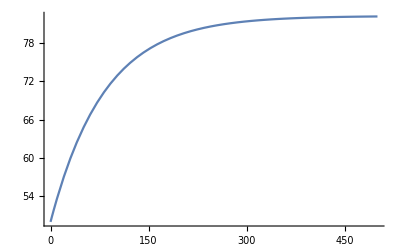

```mathematica
Plot[funkcija2[t]/.{L->165,d->0},{t,0,500},PlotRange->All]
```

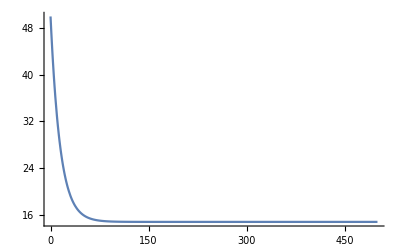

```mathematica
Plot[funkcija2[t]/.{L->30,d->0},{t,0,500},PlotRange->All]
```